## Weak-field orbital evolution via gravitational radiation reaction in Schwarzschild - de Sitter spacetime

In this notebook we show the plots of orbital trajectories for compact objects around Schwarzschild black holes influenced by an SdS parameter λ (y in this notebook). Results of this notebook has been used in Villanueva, John Adrian N., and Ian Vega. “Extreme-mass ratio inspirals in Schwarzschild-de Sitter spacetime: Weak-field orbits.” . https://journals.aps.org/prd/pdf/10.1103/npk4-61t8

We solve for the system of osculating orbital parameters,

-Graphics-

```mathematica
ClearAll["Global"]
```

```mathematica
SetDirectory[NotebookDirectory[]];

plotsFolder=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plots"}]; (*automatically saves to the plots folder in the repo*)

Get["MaTeX`"];(*MaTeX for plot generation*)
SetOptions[MaTeX,FontSize->19,"Preamble"->{"\\usepackage{newtxtext,newtxmath}"},Magnification->1.2];
style=Directive[FontFamily->"Times",FontSize->23,Black];
```

### Orbital equations:

```mathematica
fdot[p_,e_,f_,y_]:=(√(1/p^3)-y/(2 √(1/p^3)))(1+e Cos[f])^2;
deldot[p_,e_,f_,y_]:=(√(1/p^3)-y/(2 √(1/p^3)))3/p;
pdot[p_,e_,y_]:=-(8 (1-e^2)^(3/2) (8+7 e^2))/(5 p^3)+(16 (-1+e^2)+(4 (-168-283 e^2+26 e^4))/(15 (1-e^2)^(3/2))) y;
edot[p_,e_,y_]:=-(e (1-e^2)^(3/2) (304+121 e^2))/(15 p^4)+((2 (-24-965 e^2-784 e^4+73 e^6))/(15 e (1-e^2)^(3/2) p)+(32 (1-e^2)^(3/2) (-1+√(1-e^2)))/(3 e p)) y;
xpos=p[t]/(1+e[t]Cos[f[t]])Cos[f[t]+δ[t]];
ypos=p[t]/(1+e[t]Cos[f[t]])Sin[f[t]+δ[t]];
```

## Solvers

### λ = 0 vs λ=10^-7 , p=50, e=0.7

```mathematica
Clear[sol]
```

```mathematica
sol[p0_(*initial semi latus rectum*),e0_(*initial ecentricity*),y_(*sds parameter*)]:=Module[{pInit,eInit,yInit},
pInit=p0;
eInit=e0;
yInit=y;
NDSolve[{p'[t]==pdot[p[t],e[t],y],e'[t]==edot[p[t],e[t],y],f'[t]==fdot[p[t],e[t],f[t],y],δ'[t]==deldot[p[t],e[t],f[t],y],f[0]==0,e[0]==eInit,p[0]==pInit,δ[0]==0, WhenEvent[p[t]==6+2e[t],"StopIntegration"](*stop at near separatrix*)},{p,e,f,δ},{t,0,10^6(*cycles*)}][[1]]]
```

```mathematica
sol1=sol[50,0.7,0];
sol2=sol[50,0.7,10^-7];
```

Trajectory up to final time tf

```mathematica
wfsdsorb[p0_,e0_,y0_,tf0_]:=Module[{tf,p,e,y},
p=p0;
e=p0;
y=y0;
tf=tf0;
ParametricPlot[{Evaluate[{xpos,ypos}/.sol[p0,e0,0]],Evaluate[{xpos,ypos}/.sol[p0,e0,y]]},{t,0,tf},Frame->True,ImageSize->600,PlotStyle->{{Dashed,Thick,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784]},{Thick,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098]}},LabelStyle->style,FrameLabel->{MaTeX["r(\\psi) \\cos(\\phi)"],MaTeX["r(\\psi) \\sin(\\phi)"]},Epilog->{{PointSize->0.015,RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],Point[{xpos/.sol[p0,e0,0]/.t->tf,ypos/.sol[p0,e0,0]/.t->tf}]},{PointSize->0.015,RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],Point[{xpos/.sol[p0,e0,y0]/.t->tf,ypos/.sol[p0,e0,y0]/.t->tf}]}},PlotLegends->Placed[{MaTeX["\\lambda=0"],MaTeX["\\lambda="]TraditionalForm[y0//N]},{Left,Bottom}]]]
```

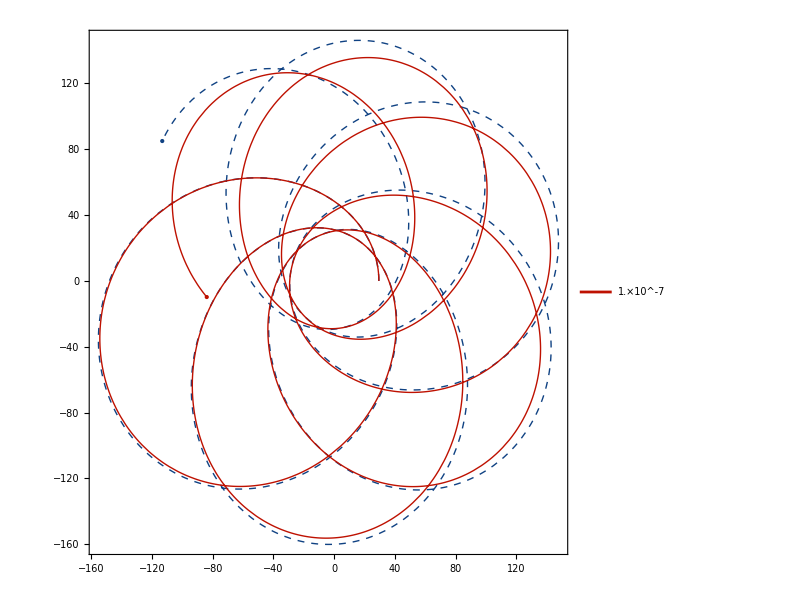

```mathematica
wfsdsorb1=wfsdsorb[50,0.7,10^-7,31000]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"orbit_50_7_-7.pdf"}]
Export[exportPath,wfsdsorb1]
```

C:\Users\Adrian Villanueva\OneDrive\Documents\GitHub\SdS-EMRI-dynamics\notebooks\plots\orbit_50_7_-7.pdf

C:\Users\Adrian Villanueva\OneDrive\Documents\GitHub\SdS-EMRI-dynamics\notebooks\plots\orbit_50_7_-7.pdf

### λ = 0 vs λ=10^-7 , p=50, e=0.4

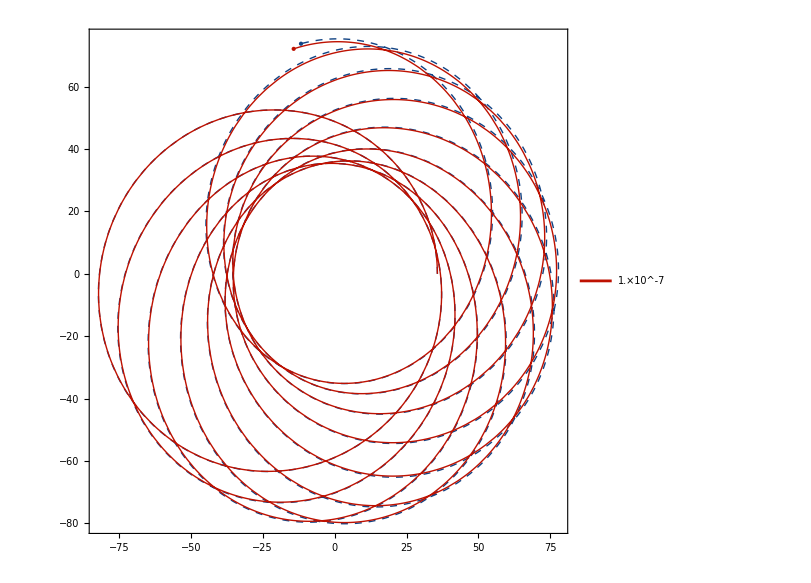

```mathematica
wfsdsorb2=wfsdsorb[50,0.4,10^-7,26000]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"orbit_50_4_-7.pdf"}];
Export[exportPath,wfsdsorb2];
```

### λ = 0 vs λ=10^-8 , p=70, e=0.7

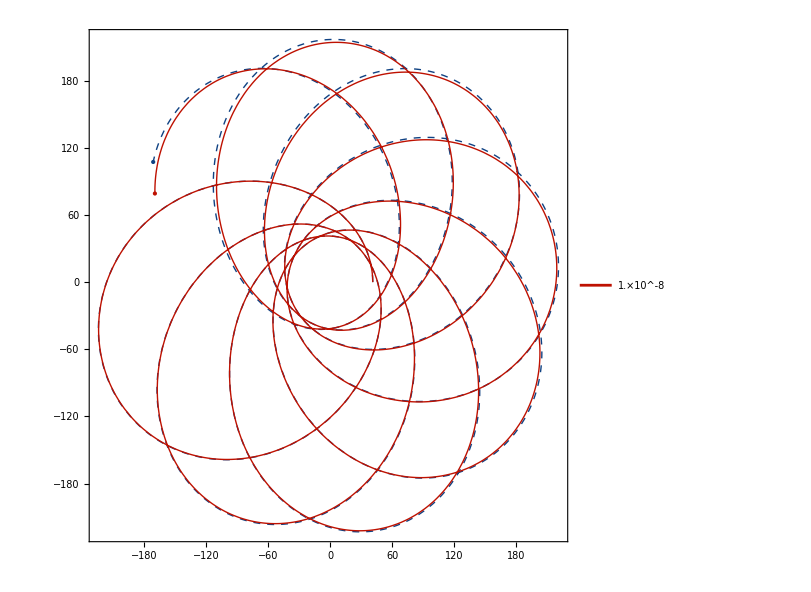

```mathematica
wfsdsorb3=wfsdsorb[70,0.7,10^-8,7.3*10^4]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"orbit_70_7_-8.pdf"}];
Export[exportPath,wfsdsorb3];
```

### λ = 0 vs λ=10^-8 , p=70, e=0.4

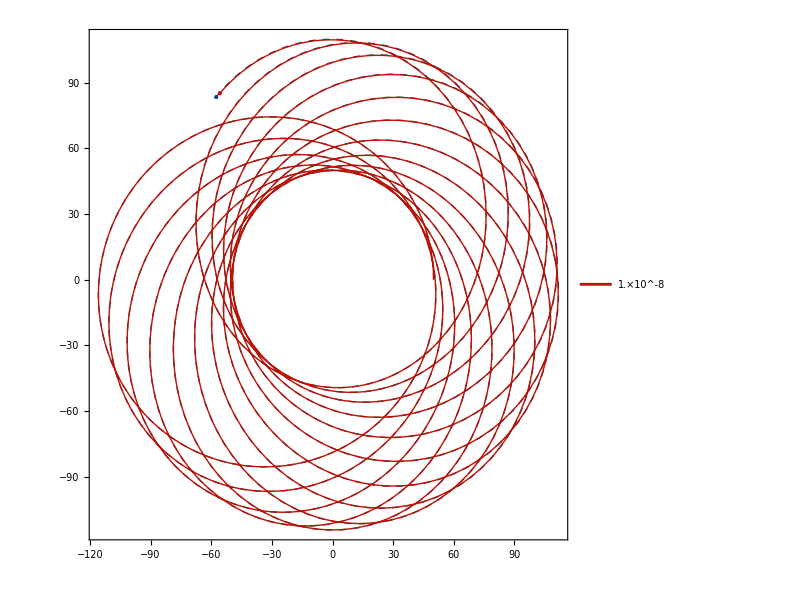

```mathematica
wfsdsorb4=wfsdsorb[70,0.4,10^-8,6.3*10^4]
```

```mathematica
exportPath=FileNameJoin[{plotsFolder,"orbit_70_4_-8.pdf"}];
Export[exportPath,wfsdsorb4];
```